## Spatially flat universe with Λ

```mathematica
Height[j0_,j1_,k_]:=√(((j0-j1)^2+8 k^2)/(2(√j0+√j1)^2));
FourVolume[j0_,j1_,k_]:=√((j0+j1)^2/32((j0-j1)^2+8 k^2));
μ[j0_,j1_,k_]:=(2+2I)√(3Pi)2^(1/4)k/(((j0-j1)^2+8 k^2)^(3/4));
SIII[j0_,j1_,k_,Λ_]:=6(j0-j1)ArcSinh[(j1-j0)/(√((j0-j1)^2+16 k^2))]+12k(Pi/2-ArcCos[(j1-j0)^2/((j0-j1)^2+16 k^2)])-Λ*FourVolume[j0,j1,k];
dSIIIdk[j0_,j1_,k_,Λ_]:=12(Pi/2-ArcCos[(j1-j0)^2/((j0-j1)^2+16 k^2)])-Λ*(√2 (j0+j1) k)/(√(j0^2-2 j0 j1+j1^2+8 k^2)); 
dSIIIdj1[j0_,j1_,j2_,k0_,k1_,Λ_]:=((j0 j1-j1^2-4 k0^2) Λ)/(2 √2 √(j0^2-2 j0 j1+j1^2+8 k0^2))-((j1^2-j1 j2+4 k1^2) Λ)/(2 √2 √(j1^2-2 j1 j2+j2^2+8 k1^2))-6 ArcSinh[(-j0+j1)/(√((j0-j1)^2+16 k0^2))]+6 ArcSinh[(-j1+j2)/(√((j1-j2)^2+16 k1^2))];
```

```mathematica
FindRoot[{dSIIIdk[10,j1,k0,0.1]==0,dSIIIdj1[10,j1,20,k0,k1,0.1]==0,dSIIIdk[j1,20,k1,0.1]==0},{{k0,3},{j1,15},{k1,2}}]
```

{k0→3.55028,j1→14.5484,k1→3.58252}

```mathematica
FindRoot[dSIIIdk[15,20,k,0.1]==0,{k,2}]
```

{k→3.26427}

```mathematica
Simplify[D[SIII[j1,j2,k1,Λ],j1],k1>0&&j1>0&&j2>0]+Simplify[D[SIII[j0,j1,k0,Λ],j1],k0>0&&j1>0&&j0>0]
```

((j0 j1-j1^2-4 k0^2) Λ)/(2 √2 √(j0^2-2 j0 j1+j1^2+8 k0^2))-((j1^2-j1 j2+4 k1^2) Λ)/(2 √2 √(j1^2-2 j1 j2+j2^2+8 k1^2))-6 ArcSinh[(-j0+j1)/(√((j0-j1)^2+16 k0^2))]+6 ArcSinh[(-j1+j2)/(√((j1-j2)^2+16 k1^2))]

```mathematica
Simplify[D[FourVolume[j0,j1,k],k],k>0&&j0>0&&j1>0]
```

(√2 (j0+j1) k)/(√(j0^2-2 j0 j1+j1^2+8 k^2))

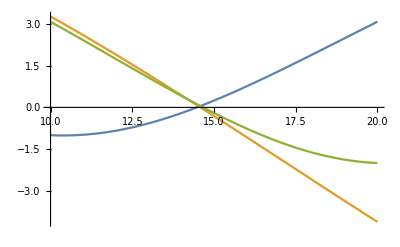

```mathematica
Plot[{dSIIIdk[10,j1,3.5,0.1],dSIIIdj1[10,j1,20,3.5,3.5,0.1],dSIIIdk[j1,20,3.5,0.1]},{j1,10,20}]
```

```mathematica
Sum[Exp[I*n^2],{n,1,Infinity}]
```

1/2 (-1+EllipticTheta[3,0,ⅇ^ⅈ])

```mathematica
Simplify[Series[SIII[j0,j1,k,Λ],{j1,Infinity,6}],Λ>0&&k>0&&j0>0]
```

-(Λ j1^2)/(4 √2)-6 ArcSinh[1] j1+(6 k π+((j0^2-4 k^2) Λ)/(4 √2)+6 j0 ArcSinh[1])-(√2 k^2 (24+j0 Λ))/j1+(√2 k^2 (-24 j0-j0^2 Λ+k^2 Λ))/j1^2+(√2 k^2 (-24 j0^2+80 k^2-j0^3 Λ+4 j0 k^2 Λ))/j1^3-(√2 k^2 (24 j0^3-240 j0 k^2+j0^4 Λ-9 j0^2 k^2 Λ+4 k^4 Λ))/j1^4-(√2 k^2 (120 j0^4-2400 j0^2 k^2+2752 k^4+5 j0^5 Λ-80 j0^3 k^2 Λ+120 j0 k^4 Λ))/(5 j1^5)+(√2 k^2 (-24 j0^5+800 j0^3 k^2-2752 j0 k^4-j0^6 Λ+25 j0^4 k^2 Λ-80 j0^2 k^4 Λ+20 k^6 Λ))/j1^6+O[1/j1]^7

```mathematica
D[μ[j0,j1,k],j1]
```

((3+3 ⅈ) 2^(1/4) (j0-j1) k √(3 π))/(((j0-j1)^2+8 k^2)^(7/4))

## Spatially spherical universe with Λ

!! Here, I use the signature (-, +, +, +) to relate to the work of Bianca, Steffen and Susanne !!

```mathematica
v1={0,l0/2,0,-l0/(2 √2)};
v2={0,-l0/2,0,-l0/(2 √2)};
v3={0,0,l0/2,l0/(2 √2)};
v4={0,0,-l0/2,l0/(2 √2)};
v5={H4,l1/2,0,-l1/(2 √2)};
v6={H4,-l1/2,0,-l1/(2 √2)};
v7={H4,0,l1/2,l1/(2 √2)};
v8={H4,0,-l1/2,l1/(2 √2)};
v1proj={H4,l0/2,0,-l0/(2 √2)};
MinProd[v_,w_]:=-v[[1]]*w[[1]]+( v[[2]]*w[[2]]+v[[3]]*w[[3]]+v[[4]]*w[[4]]);
SquaredArea[e1_,e2_]:=-1/4(MinProd[e1,e1]*MinProd[e2,e2]-(MinProd[e1,e2])^2);
l[l0_,l1_,H4_]:=√(1/8 (8 H4^2-3 (l0-l1)^2));(*strut length*)
```

```mathematica
Simplify[MinProd[v1-v5,v1-v5],H4>0&&l0>0&&l1>0]
Simplify[SquaredArea[v5-v1,v5-v6]+SquaredArea[v2-v1,v2-v6],H4>0&&l0>0&&l1>0]
```

1/8 (-8 H4^2+3 (l0-l1)^2)

1/32 (8 H4^2-(l0-l1)^2) (l0^2+l1^2)

```mathematica
Series[(2Pi-(6*600)/720 ArcSec[1/(1+x^2/2)+2]),{x,0,4}]
```

(2 π-5 ArcCos[1/3])+(5 x^2)/(12 √2)-(155 x^4)/(1152 √2)+O[x]^5

```mathematica
N[(2 π-5 ArcCos[1/3])]
```

0.128388

```mathematica
ArcCos[1/3]
```

ArcCos[1/3]